# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
pltsettings2={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->400,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
f[{a_,b_}]:=Quiet[StringReplace[ToString[TeXForm[NumberForm[SetAccuracy[a±b,Accuracy[SetPrecision[b,2]]],ExponentFunction->(Null&)]]],"."->","]]
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]][[1;;-1]]
```

{D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=30.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=32.5.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=35.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=37.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=40.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=42.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=46.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=47.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=50.2.xlsx}

```mathematica
temps=(ToExpression@StringRiffle[StringSplit[StringSplit[#,"="][[-1]],"."][[1;;-2]],"."])&/@files
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
data=SortBy[Import[#][[1]],First]&/@files;
```

## Fehler

```mathematica
σv=0.025;
σP=0.25;
```

## This is the final plot

```mathematica
(*plotMarkers->{Graphics[{Disk[{0,0},Scaled[0.02]]}],Graphics[{Disk[{0,0},Scaled[0.02]]}] }*)
```

```mathematica
states={"Gas", "Gemischt","Flüssig"}
```

{Gas,Gemischt,Flüssig}

```mathematica
plotMarkers=Charting`CommonDump`GraphicsOpenPlotMarkers[][[1;;3]];
```

```mathematica
plotMarkerAssoc=AssociationThread[states,plotMarkers];
```

```mathematica
flattened=Flatten[Map[#[[1;;3]]&, data,{2}],1];
```

```mathematica
pmarkers=plotMarkerAssoc[#[[3]]]&/@flattened;
```

```mathematica
cols=ColorData["ThermometerColors"]/@Rescale[temps];
```

```mathematica
pcolours=Flatten[Table[ConstantArray[cols[[i]],Length[data[[i]]]],{i,1,Length[data]}],1];
```

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings,Joined->True,PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours]]
```

-Graphics-

## Boundaries

```mathematica
gemischt=DeleteCases[x_/;x[[3]]!="Gemischt"]/@data;
```

```mathematica
boundaries=DeleteCases[If[#!={},{{Min[#[[All,1]]],Mean[#[[All,2]]]}, {Max[#[[All,1]]],Mean[#[[All,2]]]}}]&/@gemischt,Null]
```

{{{0.2,24.5313},{0.9,24.5313}},{{0.2,26.4615},{0.8,26.4615}},{{0.25,27.8214},{0.75,27.8214}},{{0.25,29.55},{0.7,29.55}},{{0.25,30.9688},{0.65,30.9688}},{{0.25,32.9286},{0.55,32.9286}},{{0.25,34.2083},{0.5,34.2083}},{{0.3,34.0625},{0.45,34.0625}},{{0.25,34.9},{0.45,34.9}},{{0.35,35.},{0.35,35.}}}

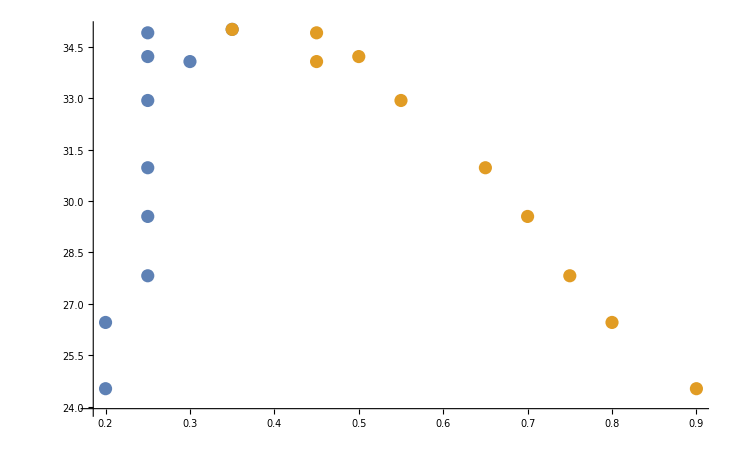

```mathematica
ListPlot[Transpose[boundaries]]
```

```mathematica
fit1=NonlinearModelFit[boundaries[[All,1]],a x^2 + b x + c,{a,b,c},x]
fit2=NonlinearModelFit[boundaries[[All,2]],a x^2 + b x + c,{a,b,c},x]
```

FittedModel[…]

FittedModel[…]

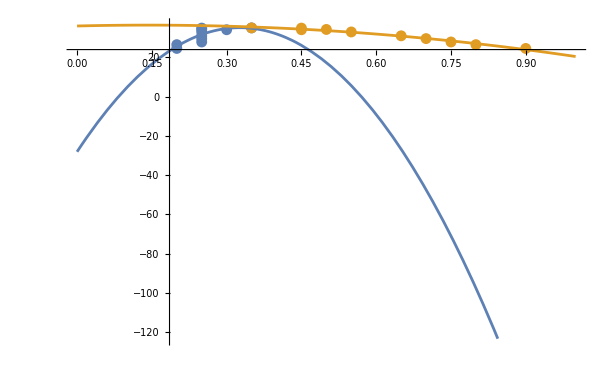

```mathematica
Show[ListPlot[Transpose[boundaries]], Plot[{fit1[x],fit2[x]},{x,0,1}],PlotRange->{All,{Automatic,36}}]
```

```mathematica
fit3=NonlinearModelFit[Flatten[boundaries,1], a x^2+ b x + c,{a,b,c},x]
```

FittedModel[…]

```mathematica
fit4=LinearModelFit[boundaries[[All,1]],x,x]
```

FittedModel[…]

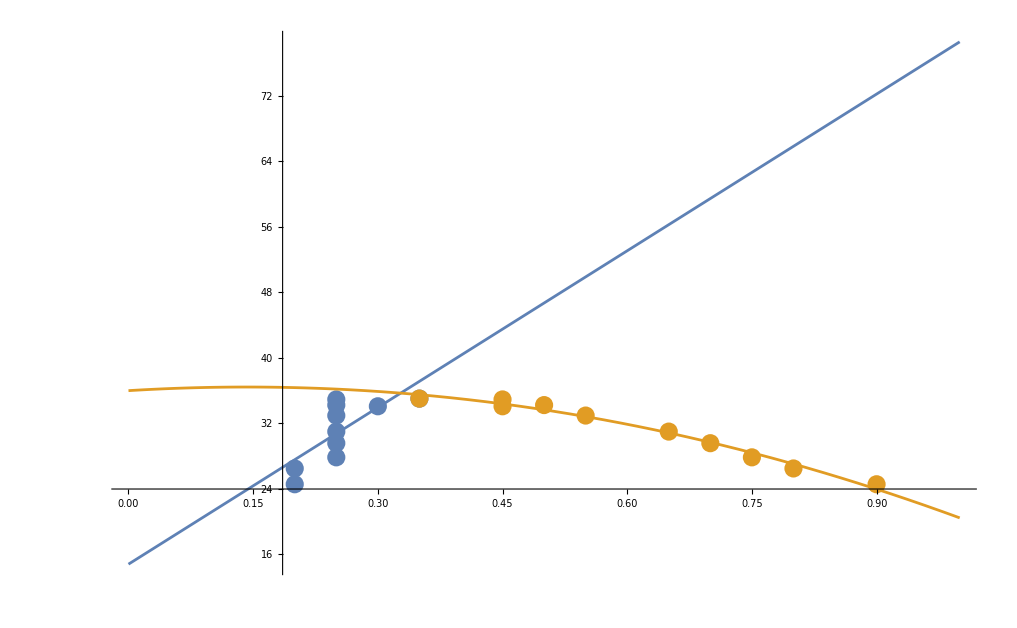

```mathematica
Show[ListPlot[Transpose[boundaries]], Plot[{fit4[x],fit2[x]},{x,0,1}],PlotRange->{All,{Automatic,36}}]
```

## Final Plots

```mathematica
intpt=SolveValues[fit4[x]==fit2[x],x][[2]]
```

0.327473

```mathematica
hval=fit2[0.95]
```

22.2331

```mathematica
x1=SolveValues[fit4[x]==hval,x][[1]]
```

0.117006

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings,Joined->True,PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours],Plot[fit2[t],{t,intpt,0.95},PlotStyle->Directive[Black,Thickness[0.003]]],Plot[fit4[t],{t,x1,intpt},PlotStyle->Directive[Black,Thickness[0.003]]]]
```

-Graphics-

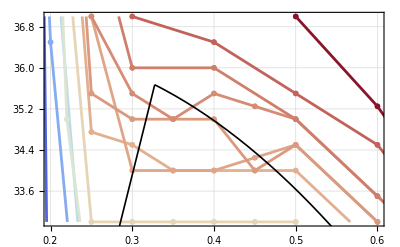

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings2,Joined->True,PlotRange->{{0.2,0.6},{33,37}}],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours],Plot[fit2[t],{t,intpt,0.95},PlotStyle->Directive[Black,Thickness[0.003]]],Plot[fit4[t],{t,x1,intpt},PlotStyle->Directive[Black,Thickness[0.003]]]]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/fig1new.pdf",Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings,Joined->True,PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours],Plot[fit2[t],{t,intpt,0.95},PlotStyle->Directive[Black,Thickness[0.003]]],Plot[fit4[t],{t,x1,intpt},PlotStyle->Directive[Black,Thickness[0.003]]]],Background->None];
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/fig1bnew.pdf",Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings2,Joined->True,PlotRange->{{0.2,0.6},{33,37}}],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours],Plot[fit2[t],{t,intpt,0.95},PlotStyle->Directive[Black,Thickness[0.003]]],Plot[fit4[t],{t,x1,intpt},PlotStyle->Directive[Black,Thickness[0.003]]]],Background->None];
```

```mathematica
Do[Export[NotebookDirectory[]<>"abbildungen/pltmarkers/plotmarker "<>ToString[i]<>".pdf",plotMarkers[[i]],Background->None],{i,1,3}]
```

## Critcal Parameters

```mathematica
temps
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
Vk=intpt*10^(-6);
ΔVk=Max[Abs[Vk-0.35*10^(-6)],Max[Vk-0.3*10^(-6)]];
Pk=fit4[intpt]*10^5;
ΔPk=Max[Abs[Pk-35*10^5],Max[Pk-36*10^5]];
Tk=(45.6+46.1)/2 + 273.15;
ΔTk=1;
```

```mathematica
f[10^6{Vk ,ΔVk}]
f[10^(-5){Pk ,ΔPk}]
f[{Tk-273.15, ΔTk}]
f[{Tk, ΔTk}]
```

0,327\pm 0,027

35,67\pm 0,67

45,9\pm 1,0

319,0\pm 1,0

```mathematica
Max[Abs[Pk-35*10^5],Max[Pk-36*10^5]]
```

```mathematica
R=8.314;
```

a = 27/(64 p) R^2 T^2

(Δa)^2 = (27/(32 p) R^2 T p ΔT)^2 +( 27/(64 p^2) R^2 T^2 Δp)^2

```mathematica
a= 27/(64 Pk) R^2 Tk^2
```

0.831915

```mathematica
Δa=Sqrt[(27/(32 Pk) R^2 Tk ΔTk)^2+(27/(64 Pk^2) R^2 Tk^2 ΔPk)^2]
```

0.0164795

```mathematica
f[{a, Δa}]
```

0,832\pm 0,016

b = RT/(8 p)

(Δb^2)=((R ΔT)/(8 p))^2+((RT Δp)/(8 p^2))^2

```mathematica
b=(R Tk)/(8 Pk)
```

0.0000929403

```mathematica
Δb=√(((R ΔTk)/(8 Pk))^2+((R Tk ΔPk)/(8 Pk^2))^2)
```

1.77056×10^-6

```mathematica
b*10^5
```

9.29403

```mathematica
10^5 Δb
```

0.177056

```mathematica
f[10^5{b, Δb}]
```

9,29\pm 0,18

n = Vk/(3 b)

Δn=√((ΔVk/(3 b))^2+((Vk Δb)/(3 b^2))^2)

```mathematica
n=Vk/(3b)
```

0.00117449

```mathematica
Δn=√((ΔVk/(3 b))^2+((Vk Δb)/(3 b^2))^2)
```

0.000101042

```mathematica
f[10^3{n, Δn}]
```

1,17\pm 0,10

```mathematica
10^3 n
10^3 Δn
```

1.17449

0.101042

```mathematica
n R Tk/(Pk Vk)
```

2.66667

```mathematica
n R Tk/(Pk Vk) Sqrt[(Δn/n)^2 + (ΔTk/Tk)^2 + (ΔPk/Pk)^2 + (ΔVk/Vk)^2]
```

0.324439